# Series sum

```mathematica
(1-Exp[-r^2 Qs2/4])/r^2
FourierTransform[%/.r->Sqrt[r1^2+r2^2],{r1,r2},{k1,k2}]/.k1->Sqrt[k^2-k2^2]//FullSimplify
```

(1-ⅇ^(-(Qs2 r^2)/4))/r^2

1/2 Gamma[0,k^2/Qs2]

```mathematica
s[a_]:=1-Exp[-a^2]
```

```mathematica
k=Sqrt[100];
nmax=30;
shift=(*3*)Pi/(4k);
a=nmax*2 Pi/k+shift; (* this is the bounday between naive integration and approximation*)
```

Try to compute this numerically

```mathematica
FourierTransform[s[r]/r^2/.r->Sqrt[r1^2+r2^2],{r1,r2},{k1,k2}]/.k1->Sqrt[k^2-k2^2]//FullSimplify
analytic=%//N//ScientificForm[#,10]&
```

-1/2 ExpIntegralEi[-25]

2.674449878×10^-13

Here the integration is done without any enhancement

```mathematica
Install["/home/tomoki/Saturation-Model/saturation-ver3/math/levin"]
```

LinkObject[…]

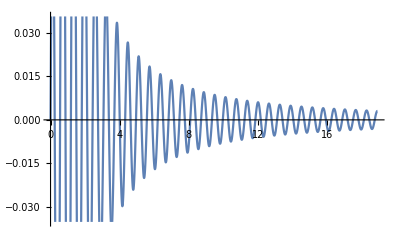

-2.62977×10^-6

```mathematica
Plot[s[r]BesselJ[0,r k]/r,{r,0, a}]
NIntegrate[s[r]BesselJ[0,r k]/r,{r,0, a}]
```

```mathematica
table={};
min=0;
max=shift;
LevinReset[]
Do[max+=Pi/k;
(*Print[Plot[s[r]BesselJ[0,r k]/r,{r,min,max}]];*)
val= NIntegrate[s[r]BesselJ[0,r k]/r,{r,min,max}];
LevinAdd[val];
AppendTo[table ,{i,val}];
min=max;
,{i,0,nmax-1}]
sum1=Map[Plus@@(table[[1;;(#[[1]]+1),2]])&,table]
```

0

{-0.000814274,-0.000236882,0.000799012,-0.00094443,0.00084416,-0.000664429,0.00049758,-0.000370976,0.000281372,-0.000218425,0.000173364,-0.000140278,0.000115388,-0.0000962636,0.0000812954,-0.0000693914,0.0000597905,-0.0000519501,0.0000454763,-0.0000400775,0.0000355348,-0.0000316812,0.0000283881,-0.0000255548,0.000023102,-0.0000209665,0.0000190974,-0.0000174534,0.0000160009,-0.0000147121}

```mathematica
sum1[[nmax]]
LevinAccel[nmax-1,0]
LevinAccel[nmax-3,2]
LevinAccel[nmax-6,5]
LevinAccel[nmax-8,7]
analytic
```

-0.0000147121

-0.0000147121

4.36555×10^-10

2.67435×10^-13

2.67438×10^-13

2.67445×10^-13

```mathematica
nmax
LevinAccel[nmax-6-14,5]
LevinSum[nmax-14]
```

30

7.64221×10^-11

0.0000597905

Now, after 15 sectors, Levin 5 point acceleration produce correct result!!!

Note if integral was done in 2Pi/k, somehow result is bad...
Also, shift=3Pi/4 is fine.

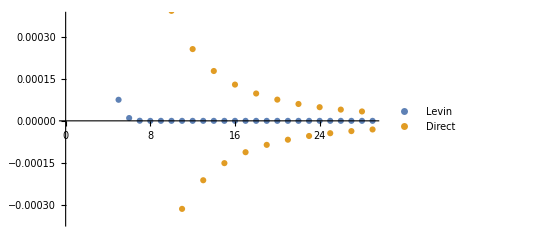

```mathematica
ltable=Table[{i-1,LevinAccel[nmax-6-(nmax-i),5]},{i,6,nmax}];
table;
ListPlot[{%%,%},PlotLegends->{"Levin","Direct" }]
```

```mathematica
ltable=Table[{i-1,LevinAccel[nmax-7-(nmax-i),6]//N[Round[#,10^(Round[Log10[Abs[#]],1]-4)]]&(*//ScientificForm[#,4]&*),table[[i,2]]//N[Round[#,10^(Round[Log10[Abs[#]],1]-4)]]&(*//ScientificForm[#,4]&*)},{i,10,30,3}]
```

{{9,-5.751×10^-9,-0.0004998},{12,-1.5891×10^-9,0.00025567},{15,-3.803×10^-11,-0.00015069},{18,6.639×10^-13,0.00009743},{21,2.6728×10^-13,-0.00006722},{24,2.6744×10^-13,0.00004866},{27,2.6744×10^-13,-0.00003655}}

```mathematica
Export["/home/tomoki/Saturation-Model/saturation-ver3/levin.dat", ltable,"Table"]
```

/home/tomoki/Saturation-Model/saturation-ver3/levin.dat

# Approximation of J0 with Cos

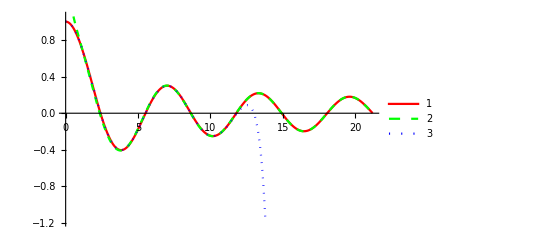

```mathematica
Plot[{BesselJ[0,r],Cos[ r+3Pi/4]/(-1.25Power[r,0.5]),Sum[(-1)^m/(Factorial[m]Gamma[m+1])(r/2)^(2m),{m,0,15}]},{r,0,3*2Pi+3Pi/4},PlotLegends->Automatic,PlotStyle->{{Red}, {Green,Dashed}, {Blue,Dotted}}]
```

```mathematica
Table[(-1)^m/(Factorial[m]Gamma[m+1])(r/2)^(2m),{m,0,5}]
```

{1,-r^2/4,r^4/64,-r^6/2304,r^8/147456,-r^10/14745600}

```mathematica
Integrate[Cos[n ArcCos[x]],{x,-1,1}]//FullSimplify[#,Assumptions->n∈Integers&&n≥0]&
```

-(1+(-1)^n)/(-1+n^2)

1000

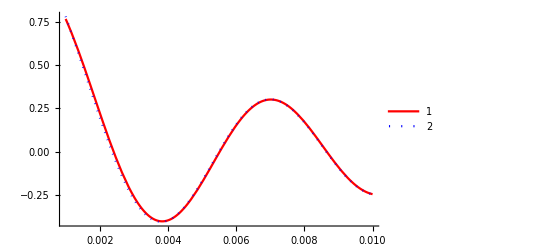

```mathematica
k=1000
Plot[{BesselJ[0,k r],Cos[ k r-Pi/4]*Sqrt[2/(Pi k r)]},{r,1/k,0.01},PlotLegends->Automatic,PlotStyle->{{Red}, {Blue,Dotted}},PlotRange->All]
```

# Old stuff

```mathematica
(*e[n_,m_,l_]:=Module[{}, 
If[m==-1,Return[0]];
If[m==0,Return[l[[n]]]];
Return[e[n+1,m-2,l]+1/(e[n+1,m-1,l]-e[n,m-1,l])]
]*)
```

```mathematica
table
```

```mathematica
table={};
min=a;
max=a;
Do[max+=(2Pi)/k;
(*Print[Plot[s[r]BesselJ[0,r k]/r,{r,min,max}]];*)
AppendTo[table ,{i, NIntegrate[s[r]BesselJ[0,r k]/r,{r,min,max}]}];
min=max;
,{i,0,25}]
table;
sum2=Map[Plus@@(table[[1;;(#[[1]]+1),2]])&,table]
(*sum1[[Length[sum1]-10;;Length[sum1]]]
Table[
Table[e[Length[sum1]-2*i-j,2*i,sum1],{i,1,2}]
,{j,0,5}]//MatrixForm*)
```

{3.54853×10^-8,6.86223×10^-8,9.96073×10^-8,1.28616×10^-7,1.55809×10^-7,1.81329×10^-7,2.05305×10^-7,2.27857×10^-7,2.49091×10^-7,2.69104×10^-7,2.87985×10^-7,3.05815×10^-7,3.22669×10^-7,3.38614×10^-7,3.53711×10^-7,3.68019×10^-7,3.81589×10^-7,3.94469×10^-7,4.06705×10^-7,4.18336×10^-7,4.29401×10^-7,4.39935×10^-7,4.49969×10^-7,4.59535×10^-7,4.68659×10^-7,4.77368×10^-7}

```mathematica
c[i_,j_,k_]:=(k+i+1)^(j-1)/(k+j+1)^(j-1);
```

```mathematica
(*levin[n_,j_,table_,sum_]:=Module[{t1,t2,total},
t1=SortBy[Table[ (-1)^i Binomial[j,i]*c[i,j,n] sum[[n+i+1 ]]/table[[n+i+1+1]],{i,0,j}],Abs];
t2=SortBy[Table[ (-1)^i Binomial[j,i]*c[i,j,n] /table[[n+i+1+1]],{i,0,j}],Abs];
total=(Plus@@t1)/(Plus@@t2);
Return[total];
]*)
```

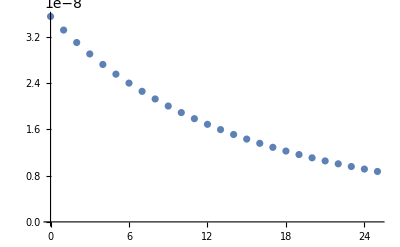

```mathematica
table//ListPlot
```

```mathematica
levin[n_,j_,table_,sum_]:=Module[{total},
total=Sum[ (-1)^i Binomial[j,i]*c[i,j,n] sum[[n+i+1 ]]/((n+i)table[[n+i+1]]),{i,0,j}]/Sum[ (-1)^i Binomial[j,i]*c[i,j,n] /((n+i)table[[n+i+1]]),{i,0,j}];
Return[total];
]
```

4

7.36452×10^-7

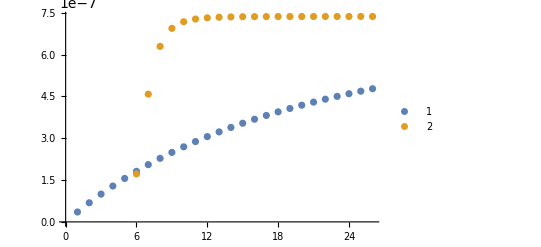

```mathematica
n=4
sum3=levin[Length[table]-n-1,n,table[[All,2]],sum2]
ListPlot[{sum2,Table[{i+n+1,levin[i,n,table[[All,2]],sum2]},{i,1,Length[table]-n-1}]},PlotLegends->Automatic]
```

```mathematica
sum1//Last
sum2//Last
sum3
Last[sum1]+sum3
analytic
```

-7.00151×10^-7

4.77368×10^-7

7.36452×10^-7

3.63014×10^-8

3.63424×10^-8

correct to three digits

## Positivity

```mathematica
Table[r,10]
```

{r,r,r,r,r,r,r,r,r,r}

(1-ⅇ^(-r^2))/r^2

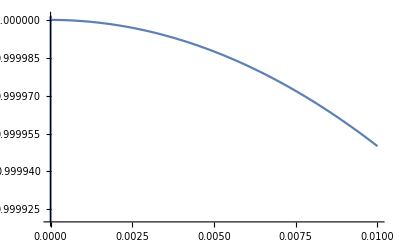

{(1-ⅇ^(-r^2))/r^2,4 ⅇ^(-r^2)-(6 (1-ⅇ^(-r^2)))/r^4+(6 ⅇ^(-r^2))/r^2,-16 ⅇ^(-r^2)+(120 (1-ⅇ^(-r^2)))/r^6-(120 ⅇ^(-r^2))/r^4-(60 ⅇ^(-r^2))/r^2-16 ⅇ^(-r^2) r^2}

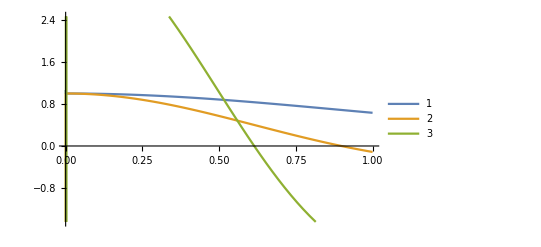

```mathematica
(1-Exp[-r^2])/r^2
Plot[%,{r,0,0.01}]
Table[(-1)^q Fold[D,(1-Exp[-r^2])/r^2,Table[r,2q]],{q,0,2}]
Plot[%,{r,0,1},PlotLegends->Automatic]
```

# BGK

```mathematica
Quit[]
```

mathlink to gluons.hh

```mathematica
Install["~/Saturation-Model/saturation-ver3/math/gluons-math"]
```

LinkObject[…]

-Graphics3D-

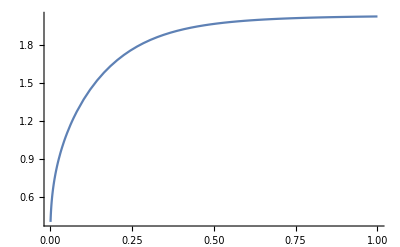

```mathematica
Plot3D[XGluon[x,Q2,1,0.2],{x,0.001,0.01},{Q2,1,1000},PlotRange->All,AxesLabel->{"x","Q2"}]
```

0.0001

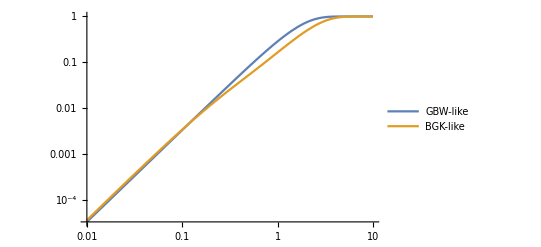

```mathematica
x=0.0001
LogLogPlot[ {(1-Exp[-r^2 (2.58*10^-4/x)^0.32/4]),(1-Exp[-r^2 Pi^2 alpha[ 0.329/r^2+1.8] XGluon[x,0.329/r^2+1.8,1.18,0.0832]/(3*23.3/0.389)])},{r,0.01,10},PlotRange->All,PlotLegends->{"GBW-like", "BGK-like"}]
```

0.00001

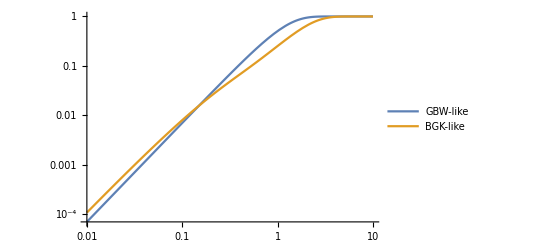

```mathematica
x=0.00001
LogLogPlot[ {(1-Exp[-r^2 (2.58*10^-4/x)^0.32/4]),(1-Exp[-r^2 Pi^2 alpha[ 0.329/r^2+1.8] XGluon[x,0.329/r^2+1.8,1.18,0.0832]/(3*23.3/0.389)])},{r,0.01,10},PlotRange->All,PlotLegends->{"GBW-like", "BGK-like"}]
```

0.00001

0

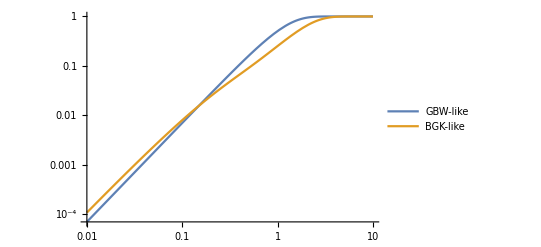

```mathematica
x=0.00001
XGluonChebInit[1.18,0.0832,x]
LogLogPlot[ {(1-Exp[-r^2 (2.58*10^-4/x)^0.32/4]),(1-Exp[-r^2 Pi^2 alpha[ 0.329/r^2+1.8] XGluonCheb[x,0.329/r^2+1.8]/(3*23.3/0.389)])},{r,0.01,10},PlotRange->All,PlotLegends->{"GBW-like", "BGK-like"}]
```

0.01

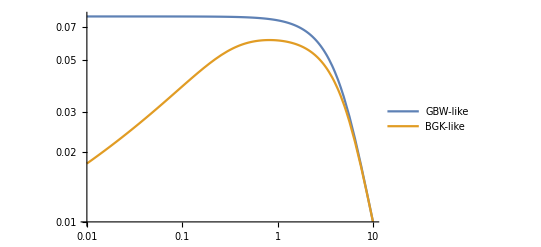

```mathematica
x=0.01
LogLogPlot[ {(1-Exp[-r^2 (2.58*10^-4/x)^0.32/4])/r^2,(1-Exp[-r^2 Pi^2 alpha[ 0.329/r^2+1.8] XGluon[x,0.329/r^2+1.8,1.18,0.0832]/(3*23.3/0.389)])/r^2},{r,0.01,10},PlotRange->All,PlotLegends->{"GBW-like", "BGK-like"}]
```

```mathematica
(*<<NumericalCalculus`*)
```

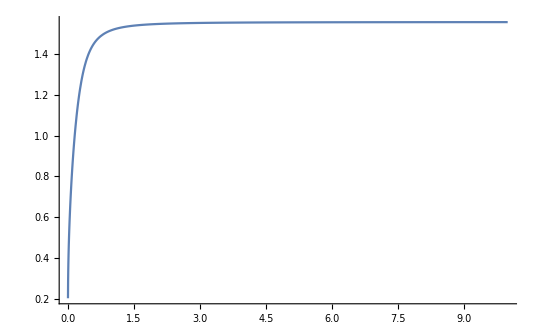

```mathematica
Plot[alpha[ 0.329/r^2+1.8]XGluon[0.01,0.329/r^2+1.8,1,0.2],{r,0.001,10},PlotRange->All]
```

```mathematica
x=0.01
```

0.01

```mathematica
(1-Exp[-r^2 Pi^2 alpha[ 0.329/r^2+1.8] XGluon[x,0.329/r^2+1.8,1.18,0.0832]/(3*23.3/0.389)])
```

1-ⅇ^(-0.0549253 r^2 alpha[1.8+0.329/r^2] XGluon[0.01,1.8+0.329/r^2,1.18,0.0832])

```mathematica
x=0.01
LogLogPlot[ {(1-Exp[-r^2 (2.58*10^-4/x)^0.32/4])/r^2,(1-Exp[-r^2 Pi^2 alpha[ 0.329/r^2+1.8] XGluon[x,0.329/r^2+1.8,1.18,0.0832]/(3*23.3/0.389)])},{r,0.01,10},PlotRange->All,PlotLegends->{"GBW-like", "BGK-like"}]
```

```mathematica
Import["/usr/local/share/tmdlib/KS-WeizWill-2017/KS-WeizWill-2017_0000.dat","Table" ]
grid2=Interpolation[Map[{{#[[1]],#[[2]]},#[[3]]}&,%]]
```

{{-18.0983,-8.99866,26.9485},{-18.0983,-8.78698,27.2949},{-18.0983,-8.5753,26.8392},{-18.0983,-8.36362,25.6724},{-18.0983,-8.15193,25.2625},{-18.0983,-7.94025,24.4334},{-18.0983,-7.72857,25.2526},4986,{-2.30259,10.6877,0},{-2.30259,10.8994,0},{-2.30259,11.111,0},{-2.30259,11.3227,0},{-2.30259,11.5344,0},{-2.30259,11.7461,0},{-2.30259,11.9578,0}}
 |  |  |  |

InterpolatingFunction[…]

```mathematica
Import["/home/tomoki/Saturation-Model/saturation-ver3/RunWW/fixa-bjorx-BGK/ww.txt","Table"]
grid=Interpolation[Map[{{#[[1]],#[[2]]},#[[3]]}&,%]]
```

{{-18.4207,-19.807,112.419},{-18.4207,-19.5186,111.036},{-18.4207,-19.2302,109.655},{-18.4207,-18.9419,108.274},{-18.4207,-18.6535,106.892},{-18.4207,-18.3651,105.511},{-18.4207,-18.0768,104.13},{-18.4207,-17.7884,102.748},{-18.4207,-17.5,101.367},14382,{0.,12.2017,1.15647×10^-20},{0.,12.4901,6.59855×10^-20},{0.,12.7785,2.80774×10^-20},{0.,13.0668,-7.39406×10^-21},{0.,13.3552,-8.2546×10^-22},{0.,13.6436,-2.09048×10^-21},{0.,13.9319,-3.63637×10^-21},{0.,14.2203,4.45733×10^-23},{0.,14.5087,-6.78645×10^-22}}
 |  |  |  |

InterpolatingFunction[…]

```mathematica
Log10[Exp[-1]]
```

-1/Log[10]

InterpolatingFunction::dmval: Input value {-2,-2.99988} lies outside the range of data in the interpolating function. Extrapolation will be used.

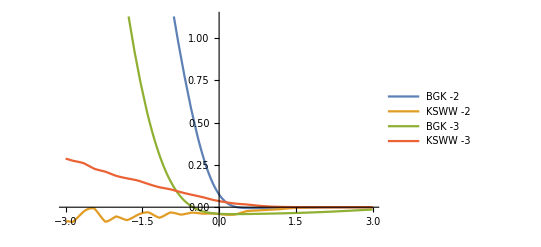

```mathematica
Plot[{0.2 grid[Log[Power[10,-2]],Log[Power[10,j]]],grid2[-2,j],grid[-2.1,j],grid2[-3,j]},{j,-3,3},PlotLegends->{"BGK -2","KSWW -2","BGK -3","KSWW -3"}]
```

## Sudakov

```mathematica
$HistoryLength=2
```

2

```mathematica
gridraw1=Import["/usr/local/share/tmdlib/KSG/GBWr.dat","Table" ];
(*grid=Interpolation[Map[{{#[[1]],#[[2]],#[[3]]},#[[4]]}&,%]]*)
grid=Interpolation[Map[{{#[[1]],#[[2]]},#[[3]]}&,gridraw1]]
gridraw2=Import["/usr/local/share/tmdlib/KSG/GBWSr.dat","Table" ];
(*grid=Interpolation[Map[{{#[[1]],#[[2]],#[[3]]},#[[4]]}&,%]]*)
grid2=Interpolation[Map[{{#[[1]],#[[2]],#[[3]]},#[[4]]}&,gridraw2]]
ClearAll[gridraw1,gridraw2]
```

InterpolatingFunction[…]

InterpolatingFunction[{{-8., 0.}, {-8.60206, 8.30103}, {-2., 3.}}, <>]

```mathematica
Plot3D[grid2[Log10[0.01],Log10[k2],m],{k2,0.01,1},{m,-1,2}]
```

-Graphics3D-

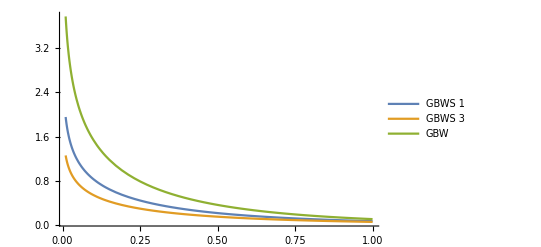

```mathematica
Plot[{grid2[Log10[0.01],Log10[k2],-1],grid2[Log10[0.01],Log10[k2],2],grid[Log10[0.01],Log10[k2]]},{k2,0.01,1},PlotRange->All,PlotLegends->{"GBWS 1","GBWS 3","GBW"}]
```

## Series sum

above ‘a’, it is approximated with Cos, and section by section it will be considered as a convergent series sum.

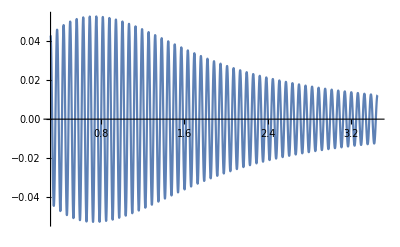

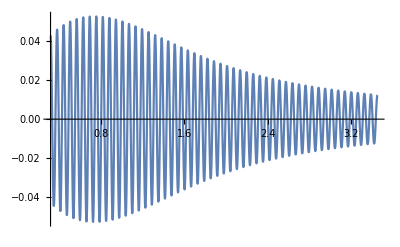

-5.84845×10^-6

-4.22718×10^-6

```mathematica
Plot[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 Sqrt[2/(Pi(k p+Pi/4))]Cos[k p],{p,a-shift,a-shift+50(2Pi)/k}]
Plot[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 BesselJ[0,(k p+Pi/4)],{p,a-shift,a-shift+50(2Pi)/k}]
NIntegrate[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 Sqrt[2/(Pi(k p+Pi/4))]Cos[k p],{p,a-shift,a-shift+50(2Pi)/k}]
NIntegrate[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 BesselJ[0,(k p+Pi/4)],{p,a-shift,a-shift+50(2Pi)/k}]
```

```mathematica
table={};
min=a-shift;
max=0;
Do[max+=(2Pi)/k;
(*Print[Plot[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 Sqrt[2/(Pi(k p+Pi/4))]Cos[k p],{p,min,max}]];*)
AppendTo[table ,{i, NIntegrate[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 Sqrt[2/(Pi(k p+Pi/4))]Cos[k p],{p,min,max}],NIntegrate[s[p+Pi/(4 k)](p+Pi/(4 k))^-1 BesselJ[0,(k p+Pi/4)],{p,min,max}]}];
min=max;
,{i,0,25}]
```

## epsilon acceleration

```mathematica
table
sum1=Map[Plus@@(table[[1;;(#[[1]]+1),2]])&,table]
sum2=Map[Plus@@(table[[1;;(#[[1]]+1),3]])&,table]
```

{{0,9.3117×10^-6,7.37374×10^-6},{1,-4.2298×10^-6,-3.29979×10^-6},{2,-2.25507×10^-6,-1.77687×10^-6},{3,-1.57511×10^-6,-1.26797×10^-6},{4,-1.25172×10^-6,-1.02912×10^-6},{5,-1.06517×10^-6,-8.9126×10^-7},{6,-9.40092×10^-7,-7.97248×10^-7},{7,-8.44862×10^-7,-7.2336×10^-7},{8,-7.6455×10^-7,-6.58603×10^-7},{9,-6.91704×10^-7,-5.97663×10^-7},{10,-6.22601×10^-7,-5.38061×10^-7},{11,-5.55529×10^-7,-4.78847×10^-7},{12,-4.89905×10^-7,-4.1992×10^-7},{13,-4.25791×10^-7,-3.61657×10^-7},{14,-3.63595×10^-7,-3.04677×10^-7},{15,-3.03892×10^-7,-2.49692×10^-7},{16,-2.47296×10^-7,-1.97413×10^-7},{17,-1.94382×10^-7,-1.4848×10^-7},{18,-1.45637×10^-7,-1.03425×10^-7},{19,-1.01427×10^-7,-6.26433×10^-8},{20,-6.1985×10^-8,-2.63909×10^-8},{21,-2.74091×10^-8,5.21891×10^-9},{22,2.33112×10^-9,3.22038×10^-8},{23,2.73792×10^-8,5.46973×10^-8},{24,4.79745×10^-8,7.29296×10^-8},{25,6.44317×10^-8,8.72065×10^-8}}

{9.3117×10^-6,5.0819×10^-6,2.82683×10^-6,1.25172×10^-6,1.73811×10^-18,-1.06517×10^-6,-2.00526×10^-6,-2.85012×10^-6,-3.61467×10^-6,-4.30637×10^-6,-4.92898×10^-6,-5.4845×10^-6,-5.97441×10^-6,-6.4002×10^-6,-6.76379×10^-6,-7.06769×10^-6,-7.31498×10^-6,-7.50936×10^-6,-7.655×10^-6,-7.75643×10^-6,-7.81841×10^-6,-7.84582×10^-6,-7.84349×10^-6,-7.81611×10^-6,-7.76814×10^-6,-7.70371×10^-6}

{7.37374×10^-6,4.07395×10^-6,2.29709×10^-6,1.02912×10^-6,-8.09763×10^-19,-8.9126×10^-7,-1.68851×10^-6,-2.41187×10^-6,-3.07047×10^-6,-3.66813×10^-6,-4.20619×10^-6,-4.68504×10^-6,-5.10496×10^-6,-5.46662×10^-6,-5.7713×10^-6,-6.02099×10^-6,-6.2184×10^-6,-6.36688×10^-6,-6.47031×10^-6,-6.53295×10^-6,-6.55934×10^-6,-6.55412×10^-6,-6.52192×10^-6,-6.46722×10^-6,-6.39429×10^-6,-6.30708×10^-6}

These are accelerated sums with different parameters. (the first one, (i=1) is Aitken-Seki delta squared )
cf. list above ‘sum’ .

```mathematica
Table[e[Length[sum1]-2*i,2*i,sum1],{i,1,5}]
Table[e[Length[sum2]-2*i,2*i,sum2],{i,1,5}]
```

{-7.95596×10^-6,-6.48671×10^-6,-6.87011×10^-6,-5.80606×10^-6,-5.85537×10^-6}

{-6.83976×10^-6,-4.9695×10^-6,-5.75078×10^-6,-4.24939×10^-6,-4.26822×10^-6}